```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+KroneckerDelta[σ,-1]KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

```mathematica
K0K0dag[ajp_,aj_,bjp_,bj_,Γ_]:=K0[ajp,aj,Γ]*K0[bj,bjp,Γ]
KiKidag[ajp_,aj_,bjp_,bj_,i_,Γ_]:=Ki[ajp,aj,i,Γ]*Ki[bjp,bj,i,Γ]
```

```mathematica
wd0[σ_,τ_,q_,p_,Γ_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,1,q}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,1,q}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q},{a1p,0,q},{b1,0,q},{b1p,0,q},{a0,0,q},{a0p,0,q},{b0,0,q},{b0p,0,q},Assumptions->{q>0,Element[q,Integers]}]
wd1[σ_,τ_,q_,p_,Γ_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]*KiKidag[a1p,a1,b1p,b1,j,Γ]+KiKidag[a0p,a0,b0p,b0,i,Γ]*KiKidag[a1p,a1,b1p,b1,j,Γ]+K0K0dag[a1p,a1,b1p,b1,Γ]*KiKidag[a0p,a0,b0p,b0,i,Γ]+K0K0dag[a0p,a0,b0p,b0,Γ]*K0K0dag[a1p,a1,b1p,b1,Γ])SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{i,1,q},{j,1,q},{a1,0,q},{a1p,0,q},{b1,0,q},{b1p,0,q},{a0,0,q},{a0p,0,q},{b0,0,q},{b0p,0,q},Assumptions->{q>0,Element[q,Integers]}]
w3[a_,b_,c_,q_,p_,Γ_]:=wd[a,1,q,p,Γ] wd[b,1,q,p,Γ]wg[c,1,q^2]+wd[a,0,q,p,Γ] wd[b,0,q,p,Γ]wg[c,0,q^2]
```

```mathematica
wdOnly[σ_,τ_,q_,p_,Γ_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q},{a1p,0,q},{b1,0,q},{b1p,0,q},{a0,0,q},{a0p,0,q},{b0,0,q},{b0p,0,q},Assumptions->{q>0,Element[q,Integers]}]
```

```mathematica
(* To check against the depolarzing channel *)
wdDepolarize[σ_,τ_,q_,p_,Γ_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,1,q}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,1,q}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2*KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,1,q},{a1p,1,q},{b1,1,q},{b1p,1,q},{a0,1,q},{a0p,1,q},{b0,1,q},{b0p,1,q},Assumptions->{q>0,Element[q,Integers]}] 
wdDepolarize[σ_,τ_,q_,p_,Γ_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,1,q}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,1,q}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2*KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}] 
w3Depolarize[a_,b_,c_,q_,p_,Γ_]:=wdDepolarize[a,1,q,p,Γ] wdDepolarize[b,1,q,p,Γ]wg[c,1,q^2]+wdDepolarize[a,-1,q,p,Γ] wdDepolarize[b,-1,q,p,Γ]wg[c,-1,q^2]
```

```mathematica
wdtest[σ_,τ_,q_,p_,Γ_]:=p^2+(1-p)^2+4(q(1-p)^2+p^2)(1-Γ)KroneckerDelta[σ,τ]+(1-Γ)^2((KroneckerDelta[σ,τ]q^2+(1-KroneckerDelta[σ,τ])q)(1-p)^2+(KroneckerDelta[σ,τ]q+(1-KroneckerDelta[σ,τ]))p^2)
wdtest[σ_,τ_,q_,p_,Γ_]:=p^2+(1-p)^2+4(1-p)^2(1-Γ)KroneckerDelta[σ,τ]+(1-Γ)^2((KroneckerDelta[σ,τ]q^2+(1-KroneckerDelta[σ,τ])q)(1-p)^2+(KroneckerDelta[σ,τ]q+(1-KroneckerDelta[σ,τ])q)p^2)
(* fixed *)
w3test[a_,b_,c_,q_,p_,Γ_]:=wdtest[a,1,q,p,Γ] wdtest[b,1,q,p,Γ]wg[c,1,q^2]+wdtest[a,0,q,p,Γ] wdtest[b,0,q,p,Γ]wg[c,0,q^2]
```

```mathematica
wdDepolarize[1,1,2,p,Γ]
wdtest[1,1,2,p,Γ]
```

(1-p)^2+p^2+2 (1-p)^2 (1-Γ)+((1-p)^2+p^2) (1-Γ)^2+2 ((1-p)^2+p^2) Γ+2 (1-p)^2 (1-Γ) Γ+((1-p)^2+p^2) Γ^2

(1-p)^2+p^2+4 (1-p)^2 (1-Γ)+(4 (1-p)^2+2 p^2) (1-Γ)^2

```mathematica
Simplify[wd0[0,0,3,p,Γ]-wd0[1,1,3,p,Γ]]
```

2 (p^2 (15-8 Γ)-6 (-2+Γ)+12 p (-2+Γ)) Γ

```mathematica
Solve[p^2 (15-8 Γ)-6 (-2+Γ)+12 p (-2+Γ)==0,p]
```

{{p→(-12+6 Γ-√6 √(-6+7 Γ-2 Γ^2))/(-15+8 Γ)},{p→(-12+6 Γ+√6 √(-6+7 Γ-2 Γ^2))/(-15+8 Γ)}}

```mathematica
wd0[0,1,2,p,Γ]-wd0[1,0,2,p,Γ]
```

-2 ((1-p)^2+p^2) Γ+4 (1-p)^2 (1-Γ) Γ-2 ((1-p)^2+p^2) (1-Γ) Γ

```mathematica
wd0[0,0,2,p,Γ]
wd0[1,1,2,p,Γ]
wd0[0,1,2,p,Γ]
wd0[1,0,2,p,Γ]
```

(1-p)^2+p^2+4 (1-p)^2 (1-Γ)+2 (1-p)^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2+2 (1-p)^2 Γ+2 ((1-p)^2+p^2) Γ+6 (1-p)^2 (1-Γ) Γ+2 ((1-p)^2+p^2) (1-Γ) Γ+2 (1-p)^2 Γ^2+2 ((1-p)^2+p^2) Γ^2

(1-p)^2+p^2+4 (1-p)^2 (1-Γ)+2 (1-p)^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2+2 ((1-p)^2+p^2) Γ^2

(1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2+4 (1-p)^2 (1-Γ) Γ+2 ((1-p)^2+p^2) Γ^2

(1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2+2 ((1-p)^2+p^2) Γ+2 ((1-p)^2+p^2) (1-Γ) Γ+2 ((1-p)^2+p^2) Γ^2

```mathematica
Simplify[4*wd0[0,0,2,p,Γ]-wd1[0,0,2,p,Γ]]
```

0

```mathematica
Simplify[wd[0,0,2,p,Γ]-wdtest[0,0,2,p,Γ]]
```

0

```mathematica
wd[0,0,3,p,Γ]
wd[0,1,3,p,Γ]
wdtest[0,0,3,p,Γ]
wdtest[0,1,3,p,Γ]
```

(1-p)^2+p^2+6 (1-p)^2 (1-Γ)+6 (1-p)^2 (1-Γ)^2+3 ((1-p)^2+p^2) (1-Γ)^2

(1-p)^2+p^2+3 ((1-p)^2+p^2) (1-Γ)^2

(1-p)^2+p^2+4 (1-p)^2 (1-Γ)+(9 (1-p)^2+3 p^2) (1-Γ)^2

(1-p)^2+p^2+(3 (1-p)^2+3 p^2) (1-Γ)^2

(1-p)^2+p^2+4 (2 (1-p)^2+p^2) (1-Γ)+(4 (1-p)^2+2 p^2) (1-Γ)^2

```mathematica
Simplify[w3[1,1,0,2,p,Γ]-w3test[1,1,0,2,p,Γ]]
```

1/60 (-45-120 Γ+104 Γ^2-32 Γ^3+4 p (45+120 Γ-104 Γ^2+32 Γ^3)-8 p^2 (45+81 Γ-62 Γ^2+18 Γ^3+2 Γ^4)+8 p^3 (45+42 Γ-20 Γ^2+4 Γ^3+4 Γ^4)-4 p^4 (45-12 Γ+40 Γ^2-24 Γ^3+12 Γ^4))

```mathematica
w3test[0,0,0,2,p,Γ]
```

-1/60 ((1-p)^2+p^2+(2 (1-p)^2+2 p^2) (1-Γ)^2)^2+1/15 ((1-p)^2+p^2+4 (1-p)^2 (1-Γ)+(4 (1-p)^2+2 p^2) (1-Γ)^2)^2

```mathematica
w3[0,0,0,2,p,Γ]
w3[1,0,0,2,p,Γ]
w3[1,1,1,2,p,Γ]
```

0

0

-1/60 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2+4 (1-p)^2 (1-Γ) Γ+2 ((1-p)^2+p^2) Γ^2)^2+1/15 ((1-p)^2+p^2+4 (1-p)^2 (1-Γ)+2 (1-p)^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2+2 (1-p)^2 Γ+2 ((1-p)^2+p^2) Γ+6 (1-p)^2 (1-Γ) Γ+2 ((1-p)^2+p^2) (1-Γ) Γ+2 (1-p)^2 Γ^2+2 ((1-p)^2+p^2) Γ^2)^2

```mathematica
K0K0dag[0,0,0,0,Γ]
```

1

```mathematica
Clear[q]
w3[0,0,0,q,p,Γ]
w3[1,0,0,q,p,Γ]
w3[0,0,1,q,p,Γ]
```

$Aborted

$Aborted

```mathematica
w3[0,0,0,4,p,Γ]
```

-(((1-p)^2+p^2+4 ((1-p)^2+p^2) (1-Γ)^2)^2)/4080+1/255 ((1-p)^2+p^2+8 (1-p)^2 (1-Γ)+12 (1-p)^2 (1-Γ)^2+4 ((1-p)^2+p^2) (1-Γ)^2)^2

```mathematica
w3[0,0,1,4,p,Γ]
w3[0,1,1,4,p,Γ]
```

1/255 ((1-p)^2+p^2+4 ((1-p)^2+p^2) (1-Γ)^2)^2-(((1-p)^2+p^2+8 (1-p)^2 (1-Γ)+12 (1-p)^2 (1-Γ)^2+4 ((1-p)^2+p^2) (1-Γ)^2)^2)/4080

1/272 ((1-p)^2+p^2+4 ((1-p)^2+p^2) (1-Γ)^2) ((1-p)^2+p^2+8 (1-p)^2 (1-Γ)+12 (1-p)^2 (1-Γ)^2+4 ((1-p)^2+p^2) (1-Γ)^2)

```mathematica
q=2;
w3[0,0,0,q,p,Γ]
w3[0,0,1,q,p,Γ]
w3[0,1,1,q,p,Γ]
w3[1,0,0,q,p,Γ]
w3[1,1,0,q,p,Γ]
w3[1,1,1,q,p,Γ]
```

2

-1/60 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2+1/15 ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2

1/15 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2-1/60 ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2

1/20 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2) ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)

1/20 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2) ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)

1/15 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2-1/60 ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2

-1/60 ((1-p)^2+p^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2+1/15 ((1-p)^2+p^2+4 p^2 (1-Γ)+2 p^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2

```mathematica
wd[0,0,3,Γ,p]
```

(1-p)^2+p^2+6 p^2 (1-Γ)+6 p^2 (1-Γ)^2+3 ((1-p)^2+p^2) (1-Γ)^2

```mathematica
Simplify[wd[0,0,3,Γ,p]]
Simplify[wd[1,0,3,Γ,p]]
Simplify[wd[0,1,3,Γ,p]]
Simplify[wd[1,1,3,Γ,p]]
```

4-6 Γ+3 Γ^2-2 p (4-6 Γ+3 Γ^2)+2 p^2 (10-15 Γ+6 Γ^2)

(1-2 p+2 p^2) (4-6 Γ+3 Γ^2)

(1-2 p+2 p^2) (4-6 Γ+3 Γ^2)

4-6 Γ+3 Γ^2-2 p (4-6 Γ+3 Γ^2)+2 p^2 (10-15 Γ+6 Γ^2)

```mathematica
Jh[q_,p_,Γ_]:=1/2 Log[w3[1,0,0,q,p,Γ]/w3[0,0,0,q,p,Γ]]
Jd[q_,p_,Γ_]:=1/2Log[w3[0,0,1,q,p,Γ]/w3[0,1,0,q,p,Γ]]
```

```mathematica
q=2;
(* Condition on the transition *)
Solve[2w3[0,1,0,q,p,Γ]==w3[0,0,0,q,p,Γ]-w3[0,0,1,q,p,Γ]
,{p,Γ}](*NSolve[2 w3[0,1,0,q,p,Γ]/w3[0,0,0,q,p,Γ]==w3[0,1,0,q,p,Γ]/w3[0,0,1,q,p,Γ] -w3[0,0,1,q,p,Γ]/w3[0,1,0,q,p,Γ],{p,Γ}, Reals]*)
```

Solve[2 w3[0,1,0,2,p,Γ]==w3[0,0,0,2,p,Γ]-w3[0,0,1,2,p,Γ],{p,Γ}]

```mathematica
N[Sin[ArcTan[(5/(Sqrt[34]-2)-1)^(1/4)]]^2]
```

0.355841

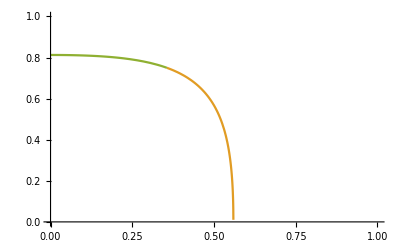

```mathematica
w3000q2=w3[0,0,0,2,p,Γ];
w3010q2=w3[0,1,0,2,p,Γ];
w3001q2=w3[0,0,1,2,p,Γ];
Plot[Γ/.NSolve[{2w3010q2==w3000q2-w3001q2}/.{p->p0},{Γ}]//Evaluate,{p0,0,1},PlotRange->{{0,1},{0,1}}]
```

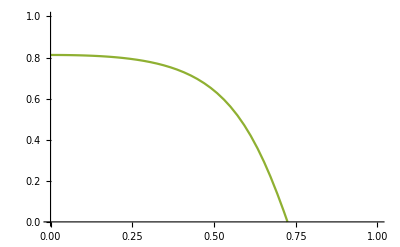

```mathematica
w3000q2=w3test[0,0,0,2,p,Γ];
w3010q2=w3test[0,1,0,2,p,Γ];
w3001q2=w3test[0,0,1,2,p,Γ];Plot[Γ/.NSolve[{2w3010q2==w3000q2-w3001q2}/.{p->p0},{Γ}]//Evaluate,{p0,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
q=3;
w3000q3=w3[0,0,0,q,p,Γ];
w3010q3=w3[0,1,0,q,p,Γ];
w3001q3=w3[0,0,1,q,p,Γ];
```

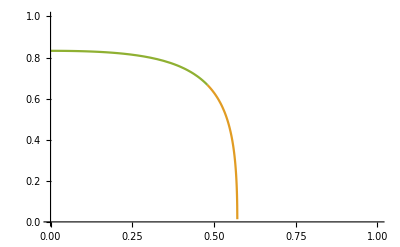

```mathematica
Plot[{Γ/.NSolve[{2w3010q2==w3000q2-w3001q2}/.{p->p0},{Γ}]//Evaluate,Γ/.NSolve[{2w3010q3==w3000q3-w3001q3}/.{p->p0},{Γ}]//Evaluate},{p0,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
Clear[Γ]
NSolve[2w3Depolarize[0,1,0,q,p,Γ]==w3Depolarize[0,0,0,q,p,Γ]-w3Depolarize[0,0,1,q,p,Γ],{p,Γ}, Reals]
```

{{p→-2.97986,Γ→1.},{p→-2.97986,Γ→1.},{p→-2.97986,Γ→1.},{p→-2.97986,Γ→1.},{p→0.355841,Γ→-1.18669},{p→-1.2342,Γ→-0.144354}}

```mathematica
diff=1/10 ((1-p)^2+p^2) (2 (1-p)^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2) (1-Γ)^2*2-(1/12 (2 (1-p)^2 (1-Γ)^2+2 ((1-p)^2+p^2) (1-Γ)^2)^2-1/3 ((1-p)^2+p^2)^2 (1-Γ)^4);
f1=z;
```

```mathematica
ContourPlot3D[{diff==0,f1==0},{p,0,1},{Γ,0,1},{z,-0.5,0.5},MeshFunctions->{Function[{p,Γ,z},diff-f1]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]],AxesLabel->{"p","Γ","z"},LabelStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
q=2;
diff2=2w3[0,1,0,q,p,Γ]-(w3[0,0,0,q,p,Γ]-w3[0,0,1,q,p,Γ]);
```

```mathematica
ContourPlot3D[{diff2==0,f1==0},{p,0,1},{Γ,0,1},{z,-0.5,0.5},MeshFunctions->{Function[{p,Γ,z},diff2-f1]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Green,Opacity[0.5],Specularity[White,30]],AxesLabel->{"p","Γ","z"},LabelStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
q=2;
diff2test=2w3test[0,1,0,q,p,Γ]-(w3test[0,0,0,q,p,Γ]-w3test[0,0,1,q,p,Γ]);
ContourPlot3D[{diff2test==0,z==0},{p,0,10},{Γ,0,10},{z,-5,5},MeshFunctions->{Function[{p,Γ,z},diff2-z]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Green,Opacity[0.5],Specularity[White,30]],AxesLabel->{"p","Γ","z"},LabelStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
q=3;
diff3=2w3[0,1,0,q,p,Γ]-(w3[0,0,0,q,p,Γ]-w3[0,0,1,q,p,Γ]);
ContourPlot3D[{diff3==0,f1==0},{p,0,1},{Γ,0,1},{z,-0.5,0.5},MeshFunctions->{Function[{p,Γ,z,f},diff3-f1]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]],AxesLabel->{"p","Γ","z"},LabelStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
Plot3D[2w3Depolarize[0,1,0,q,p,Γ] -(w3Depolarize[0,0,0,q,p,Γ]-w3Depolarize[0,0,1,q,p,Γ]),{p,0,1},{Γ,0,1}]
```

$Aborted

```mathematica
q=4;
Γ=0;
(* Condition on the transition *)
NSolve[2w3[0,1,0,q,p,Γ]/Sqrt[w3[0,0,1,q,p,Γ]w3[0,0,0,q,p,Γ] ]==Sqrt[w3[0,0,0,q,p,Γ]/w3[0,0,1,q,p,Γ]]-Sqrt[w3[0,0,1,q,p,Γ]/w3[0,0,0,q,p,Γ]]
,{p}, Reals]
```

$Aborted

```mathematica
q=4;
(* Condition on the transition *)
NSolve[2 w3[0,1,0,q,p,Γ]/w3[0,0,0,q,p,Γ]==w3[0,1,0,q,p,Γ]/w3[0,0,1,q,p,Γ] -w3[0,0,1,q,p,Γ]/w3[0,1,0,q,p,Γ],{p,Γ}, Reals]
```

{{p→-2.73624,Γ→2.71962},{p→-1.43712,Γ→0.737862},{p→0.307884,Γ→-1.92407},{p→-0.724544,Γ→-0.349139}}

```mathematica
N[92291/87992]
N[121001/175984]
```

1.04886

0.687568